```mathematica
KneserGirth[n_,r_]:=Min[If[n==2r+1,6,4],2Ceiling[r/(n-2r)]+1]
```

```mathematica
MaxEdges[n_,g_,low_]:=MaximalBy[Select[Import["graph"<>ToString[n]<>"c.g6"],EdgeCount[#]≥low&&FindCycle[#,g-1]=={}&],EdgeCount];
MaxEdges[n_,g_]:=MaxEdges[n,g,n]
```

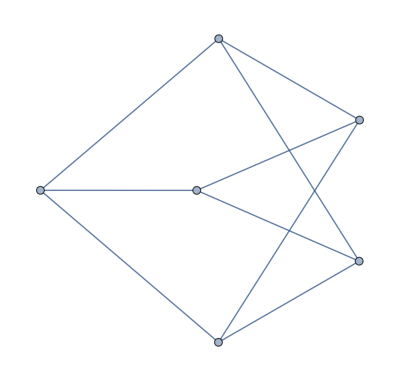
{-Graphics-,9}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[6,4]]
```

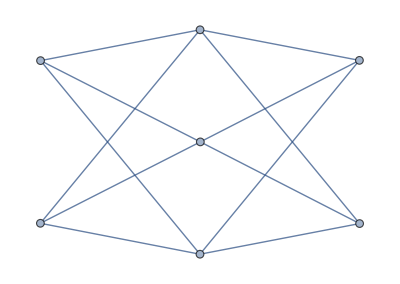
{-Graphics-,12}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[7,4]]
```

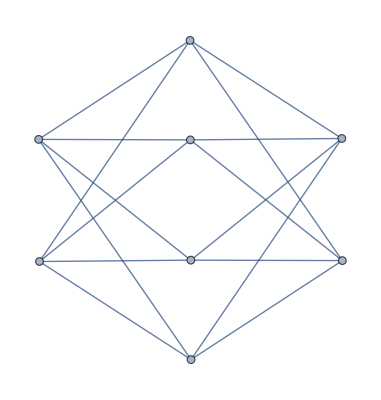
{-Graphics-,16}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[8,4]]
```

```mathematica
KneserGirth[9,4]
```

6

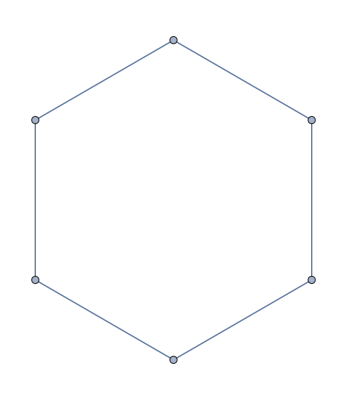
{-Graphics-,6}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[6,6]]
```

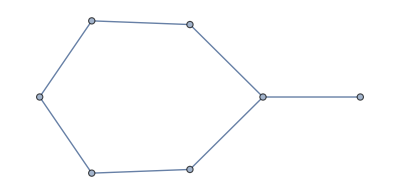
{-Graphics-,7}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[7,6]]
```

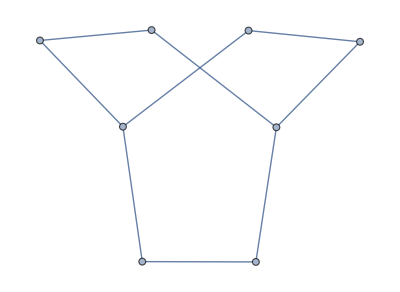
{-Graphics-,9}

```mathematica
{#,EdgeCount[#]}&[First@MaxEdges[8,6]]
```